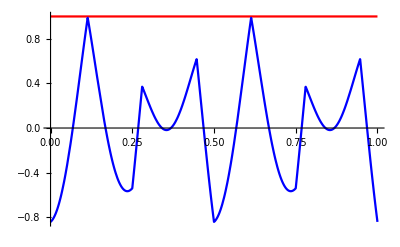

```mathematica
(*清除所有变量*)ClearAll["Global`*"]

tEnd=20;

{thetassol,wssol,tElecSsol,triggerSsol}=NDSolveValue[{thetas'[t]==ws[t],
ws'[t]==tElecS[t],
tElecS[t]==-triggerS[t]*Abs[-Sin[2*Pi*2*t]+Sin[2*Pi*3*t+1]],
triggerS[t]==1,

(*初始条件*)thetas[0]==0,ws[0]==100,tElecS[0]==-Sin[1],triggerS[0]==1,

(*判定条件*)WhenEvent[Abs[Sin[2*Pi*2*t]]>Abs[Sin[2*Pi*3*t+1]],{triggerS[t]=0}]},
{thetas,ws,tElecS,triggerS},{t,0,tEnd}];

Plot[{triggerSsol[t],Abs[Sin[2*Pi*2*t]]-Abs[Sin[2*Pi*3*t+1]]},{t,0,1},PlotStyle->{Red,Blue}](*蓝色曲线高于x轴时红色曲线应当为y=0，但实际上一直在y=1，是WhenEvent用错了吗*)
```